# reverse engineering a worm’s mind

## what a pretentious title!

revisiting the psychophysics of c. elegans

## background

### by way of warning

anything with a capital letter (change script?) should be taken to be written in “scare quotes.” this denotes really useful words with ambiguous definitions. not all scary words are marked as such!

### behavioral psych

#### what is it?

```mathematica
Graphics[] (* of a 'black box' model *)
```

A Mind is a Black Box which maps Inputs onto Outputs. Inputs and Outputs should be easily observed and quantified. As such, it is a collection of rules.

#### what is input?

```mathematica
Graphics[]
```

easily quantified: external sensory stimuli
maybe easily quantified: internal sensory stimuli (hungry, sexy, etc.)
not easily quantified: thoughts? feelings? memory? “internal state?”

#### what is output?

```mathematica
Graphics[]
```

easily quantified : movement, stereotyped behaviors
maybe easily quantified: nonstereotyped observable behavior (vocalization, goal-directed crap etc.)
not easily quantified: thoughts, feelings, “internal state,” memory and altered future behavior

#### what is the black box?

```mathematica
Graphics[]
```

so far, we’ve resisted calling it a “function.” this is because most black boxes that we construct are really incomplete (this doesn’t mean they’re not useful). let’s just take this for granted; obviously nobody’s able to model even a small part of this in any realistic fashion.

it’s an empirically-derived set of rules.

laura hears | laura says | probability | notes
"hi laura!" | "hi nate" | 0.95 | pretty robust
"hi laura!" | "eat shit 'n die!" | 0.025 | ????? hypothesis: related to missed birthday or anniversary?
"hi laura!" | "hi billy-bob" | 0.005 | edge case-- need to control for stimulus delivery!
"hi laura!" | "hi joe" | 0.005 | edge case-- typically happens when undergrads are doing it or something
"hi laura!" | ... | ... | ...

this doesn’t seem very rigorous!

the Black Box also abstracts away all of the biology in between Input and Output. (graphics: black box becoming a mess of fibers and neurons)

let’s explore this a little more.

movement and body shape result from patterns (𝓍⃗,𝓉) of muscle contraction. (graphics?)

which result from patterns of Activity in the innervating motor neurons (graphics?)

which result from patterns of Activity in the innervating interneurons (graphics?)

which result from patterns of Activity in the innervating sensory neurons (graphics?)

by way of analogy,

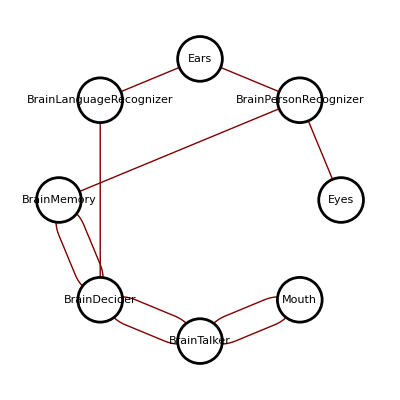

```mathematica
Graphics[mindOfLauraGraphPlot] (* of Laura's eyes/ears -> memory -> vocal stuff -> mouth *)
```

this is starting to get complicated, and this is even before getting down to the level of electrical signals and chemical signaling!

fortunately, there’s a simpler model.

### nematode physiology

```mathematica
Graphics[]
```

this is c. elegans, an elegant little worm.

ze’s got ### muscles controlled by #### neurons

however, these are grouped into ####...

```mathematica
Graphics[]
Graphics[]
Graphics[]
```

### eigenworms

in real life, body shapes are constrained. body shapes are comfined to a plane (as body muscles only have planar symmetry) and muscles cannot stretch or contract infinitely.

```mathematica
Graphics[] (* a ridiculously splayed out body *)
```

90% of body shape variance is described by just 4 characteristic body shapes

```mathematica
Graphics[] (* ryu's graphic from the thin paper! *)
```

in other words, most body shapes are generated from a small number of characteristic, invariant patterns of muscle contraction/motor neuron activation.

This of course is a rough estimate of a “whole worm,” because we’re missing:
-pharynx muscles (chewing and swallowing)
-3d head movements
-egging and mating

but maybe it’s enough for drug screening, if not for a complete theory of mind.